## The static magnetic moments μ_I evaluated according to the definition -Graphics-

```mathematica
ClearAll["Global`*"]
```

```mathematica
A=163;
Z=71;
gR=Z/A;
muI[I_,K_,x_]:=gR*I+x*K^2/(I+1);
diff[BM1_,I_,K_]:=√((4π)/3)(BM1/(K^2*(ClebschGordan[{I,K},{1,0},{I-1,K}])^2))^(1/2);
```

```mathematica
BM1th={0.017,0.018,0.019,0.019,0.020};
BM1exp={0.017,0.017,0.024,0.023,0.024};
spins=Table[i/2,{i,47,63,4}];
gprimesTh[K_]:=Table[diff[BM1th[[i]],spins[[i]],K]*100,{i,1,Length[BM1th]}];
gprimesExp[K_]:=Table[diff[BM1exp[[i]],spins[[i]],K]*100,{i,1,Length[BM1exp]}];
muITh=Table[muI[spins[[i]],spins[[i]]-1,diff[BM1th[[i]],spins[[i]],spins[[i]]-1]],{i,1,Length[BM1th]}];
muIExp=Table[muI[spins[[i]],spins[[i]]-1,diff[BM1exp[[i]],spins[[i]],spins[[i]]-1]],{i,1,Length[BM1exp]}];
```

```mathematica
muITh
muIExp
```

{11.4498,12.4147,13.3794,14.306,15.2698}

{11.4498,12.3779,13.5529,14.4519,15.4176}

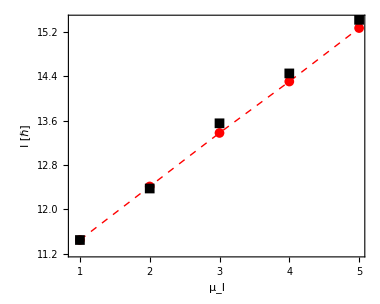

```mathematica
ListPlot[{muITh,muIExp},PlotRange->Full,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],AspectRatio->0.8,ImageSize->380,PlotMarkers->{Automatic, Medium},Joined->{True,False},PlotStyle->{{Red,Thick,Dashed},{Black,Thick}},FrameLabel->{"μ_I","I [ℏ]"}]
```